# Higgs-Gluon Form Factor

We prepare the Data for the Higgs-Gluon Form Factor. The results are taken from Czakon and Niggetiedt, 2020

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<ggHCzakonNiggetiedt.m
```

## Compare my Results and Expand

```mathematica
c0[z_]:= 1/2 1/z (1 - (1 - 1/z) (1/2 Log[(√(1 - 1/z) - 1)/(√(1 - 1/z) + 1)])^2);
```

```mathematica
myC0Re = Plot[Re[c0[z]], {z, 0.01, 4}, PlotStyle->Red, PlotRange->All];
theirC0Re = Plot[Re[C0[z]], {z, 0.01, 4}, PlotStyle->Green];
myC0Im = Plot[Im[c0[z]], {z, 0.01, 4}, PlotStyle->Red, PlotRange->All];
theirC0Im = Plot[Im[C0[z]], {z, 0.01, 4}, PlotStyle->Green];
myC0Abs = Plot[Abs[c0[z]], {z, 0.01, 10}, PlotStyle->Red, PlotRange->{{0,10},{0, 1}}];
```

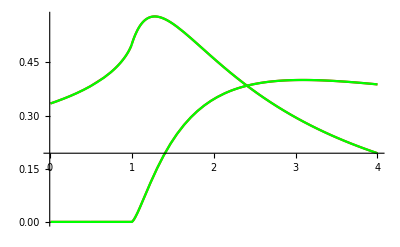

```mathematica
Show[myC0Re, theirC0Re, myC0Im, theirC0Im]
```

Large mass expansion

```mathematica
LME = Series[c0[z], {z, 0, 1}]//Normal
```

1/3+(7 z)/90

```mathematica
LMEPlot =Plot[Abs[LME], {z, 0.01, 10}, PlotStyle->Blue,PlotRange->{{0,10},{0, 1}}];
```

High energy expansion

```mathematica
HEL = Series[c0[1/ρ], {ρ, 0, 2}] //Normal
```

1/8 ρ (4-Log[-ρ/4]^2)+1/8 ρ^2 (-Log[-ρ/4]+Log[-ρ/4]^2)

```mathematica
HELPlot = Plot[Abs[HEL]/.{ρ -> 1/z}, {z, 0.01, 10}, PlotStyle->Green, PlotRange->{{0,10},{0, 1}}];
```

Threshold Expansion

```mathematica
PadeApproximant[2 Pi (1 - z)^(3/2)/4/.{z-> (4ω)/(1 + ω)^2}, {ω, 1, {4, 4}}]
```

(π ((-1+ω)^2)^(3/2))/(16 (1+3/2 (-1+ω)+3/4 (-1+ω)^2+1/8 (-1+ω)^3))

```mathematica
Solve[z==(4 ω)/(1 + ω)^2, ω]
```

{{ω→(2-2 √(1-z)-z)/z},{ω→(2+2 √(1-z)-z)/z}}

```mathematica
TE3 = 1/2+1/8 (-4+π^2) (-1+z)+(π ((-1+ω)^2)^(3/2))/(16 (1+3/2 (-1+ω)+3/4 (-1+ω)^2+1/8 (-1+ω)^3)) /.{ω->(2+2 √(1-z)-z)/z}
```

1/2+(π ((-1+(2+2 √(1-z)-z)/z)^2)^(3/2))/(16 (1+3/2 (-1+(2+2 √(1-z)-z)/z)+3/4 (-1+(2+2 √(1-z)-z)/z)^2+1/8 (-1+(2+2 √(1-z)-z)/z)^3))+1/8 (-4+π^2) (-1+z)

```mathematica
TE2 =Assuming[z>0&&ρ>0 && z < 1, Series[c0[z], {z, 1, 1}]]//Normal
```

1/2+1/8 (-4+π^2) (-1+z)+1/2 ⅈ π (-1+z)^(3/2)

```mathematica
TE1 =Assuming[z>0&&ρ>0, Series[c0[1/ρ], {ρ, 1, 2}]]//Normal
```

Piecewise[{{1/2+1/8 (4-π^2) (-1+ρ)-1/2 ⅈ π √(1-ρ) (-1+ρ)+1/8 (-4-π^2) (-1+ρ)^2-1/3 ⅈ π √(1-ρ) (-1+ρ)^2, Im[2 √(1-ρ)-2 √(1-ρ) (-1+ρ)]≥0}, {1/2+1/8 (4-π^2) (-1+ρ)+1/2 ⅈ π √(1-ρ) (-1+ρ)+1/8 (-4-π^2) (-1+ρ)^2+1/3 ⅈ π √(1-ρ) (-1+ρ)^2, True}}]

```mathematica
TE1Plot = Plot[Abs[TE1]/.{ρ-> 1/z}, {z, 0, 4}, PlotStyle->Dashed];
TE2Plot = Plot[Abs[TE2]/.{ρ-> 1/z}, {z, 0, 4}, PlotStyle->Black]; 
TE3Plot = Plot[Abs[TE3], {z, 0, 4}, PlotStyle->Dotted];
```

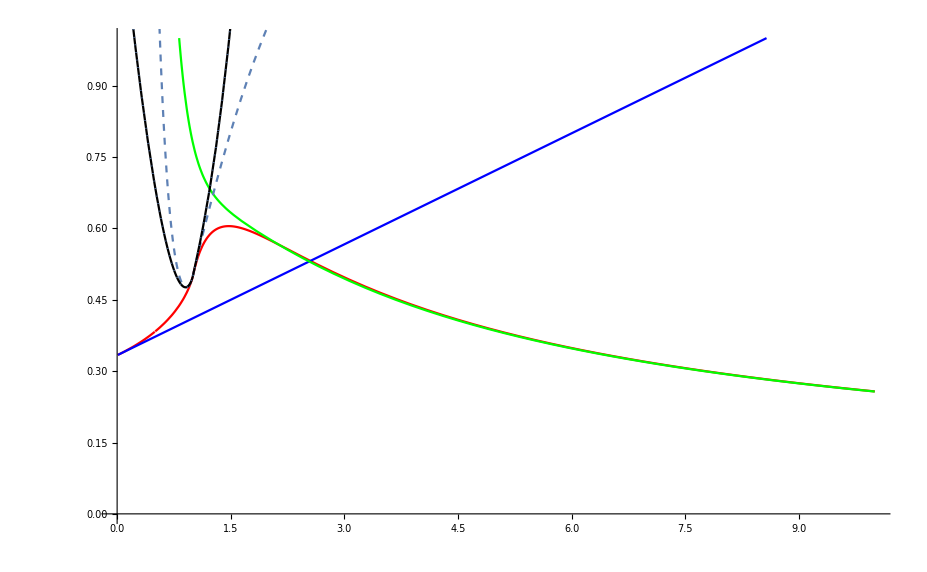

```mathematica
Show[myC0Abs, LMEPlot, HELPlot, TE1Plot, TE2Plot, TE3Plot]
```

## Plot Data

```mathematica
LORePlot = Plot[Re[C0[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle->Green];
NLORePlot = Plot[Re[C1I[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle-> Blue];
NNLORePlot = Plot[Re[C2I[z, 5]]/10, {z, 0.01, 4}, PlotRange->All,PlotStyle->Red];
```

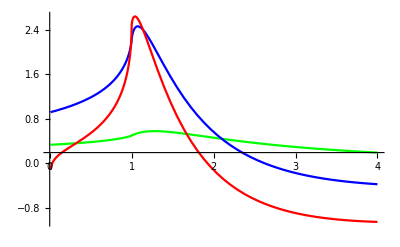

```mathematica
Show[LORePlot, NLORePlot, NNLORePlot]
```

```mathematica
LORePlotZ = Plot[Re[Coefficient[CZ[z, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 0]], {z, 0.01, 4}, PlotRange->All, PlotStyle->Green];
NLORePlotZ = Plot[Re[Coefficient[CZ[z, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 1]], {z, 0.01, 4}, PlotRange->All, PlotStyle-> Blue];
NNLORePlotZ = Plot[Re[Coefficient[CZ[z, nl,Lmu]/.{nl-> 5, Lmu-> 0},api, 2]]/10, {z, 0.01, 4}, PlotRange->All,PlotStyle->Red];
```

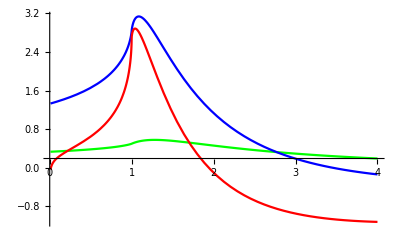

```mathematica
Show[LORePlotZ, NLORePlotZ, NNLORePlotZ]
```

```mathematica
LOImPlot = Plot[Im[C0[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle->Green];
NLOImPlot = Plot[Im[C1I[z]], {z, 0.01, 4}, PlotRange->All, PlotStyle-> Blue];
NNLOImPlot = Plot[Im[C2I[z, 5]]/10, {z, 0.01, 4}, PlotRange->All,PlotStyle->Red];
```

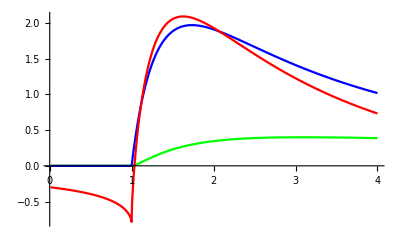

```mathematica
Show[LOImPlot, NLOImPlot, NNLOImPlot]
```

```mathematica
LOImPlotZ = Plot[Im[Coefficient[CZ[z, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 0]], {z, 0.01, 4}, PlotRange->All, PlotStyle->Green];
NLOImPlotZ = Plot[Im[Coefficient[CZ[z, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 1]], {z, 0.01, 4}, PlotRange->All, PlotStyle-> Blue];
NNLOImPlotZ = Plot[Im[Coefficient[CZ[z, nl,Lmu]/.{nl-> 5, Lmu-> 0},api, 2]]/10, {z, 0.01, 4}, PlotRange->All,PlotStyle->Red];
```

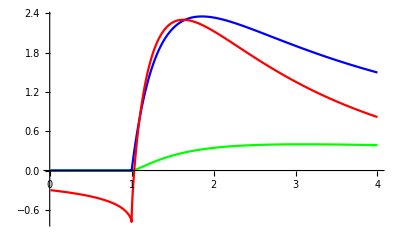

```mathematica
Show[LOImPlotZ, NLOImPlotZ, NNLOImPlotZ]
```

## Export Data to CSV file

```mathematica
(*Define the function to export data points and their corresponding function values*)
ExportDataPoints[fileName_,array_,func_]:=Module[{dataPairs},
(*Create pairs of data points and function values*)
dataPairs=Table[{array[[i]],func[array[[i]]]},{i,1,Length[array]}];
(*Export the data pairs to a file*)
Export[fileName,dataPairs,"CSV"];]
```

```mathematica
1/(4*4^2/125^2)//N
```

244.141

```mathematica
RangeLo
```

```mathematica
zs = Join[Range[0.01, 2, 0.01], PowerRange[2, 300, 1.05]];
```

```mathematica
ExportDataPoints["LO_Re.csv", zs, Re[Coefficient[CZ[#, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 0]]&];
ExportDataPoints["NLO_Re.csv", zs,  Re[Coefficient[CZ[#, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 1]]&];
ExportDataPoints["NNLO_Re.csv", zs, Re[Coefficient[CZ[#, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 2]]&];
ExportDataPoints["LO_Im.csv", zs,  Im[Coefficient[CZ[#, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 0]]&];
ExportDataPoints["NLO_Im.csv", zs,  Im[Coefficient[CZ[#, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 1]]&];
ExportDataPoints["NNLO_Im.csv", zs,  Im[Coefficient[CZ[#, nl, Lmu]/.{nl-> 5, Lmu-> 0}, api, 2]]&];
```

General::munfl: 1/(-1.5+0.866025 ⅈ)^3 is too small to represent as a normalized machine number; precision may be lost.

## Evaluate LO Cross Section

```mathematica
unit = ℏ^2 c^2/((10^9 e)^2) 10^12 10^28 /.{ℏ ->(6.62607015*^-34)/(2 Pi), c ->  299792458, e-> 1.60217663*^-19} (*conversion factor from 1/GeV^2 to pb*)
```

3.89379×10^8

```mathematica
Lgg = 275.2448947572225;(* Gluon-Gluon luminosity at mH^2/S *)
```

```mathematica
numerics = {mH -> 125, mt-> √(23/12) mH, mb-> 4.18, mc-> 1.27, alphas -> 0.125157,GF-> 1.16637 10^-5, v-> 1/(√(√2 GF)), COM -> 13000, d-> 4, Nc -> 3};(* alphas was computed with LHAPDF see programs/c++/decoupling/main.cpp *)
```

```mathematica
results = {};
mQ = {mt, mb, mc};
Do[resultsj={};
Do[If[i==j,combinatorics=1, combinatorics=2];
M2=alphas^2/Pi^2 1/v^2 (Nc^2 - 1) (mH^2/2)^2(d - 2)combinatorics Re[Conjugate[ C0[mH^2/(4 mQ[[i]]^2)]]C0[mH^2/(4 mQ[[j]]^2)]];
M2Bar = M2/(2^2 (Nc^2 - 1)^2);
σHat = 1/(2 mH^2) (2 Pi)/COM^2 M2Bar;
σ = N[Lgg COM^2/mH^2 σHat //.numerics];
Print[i,",", j, ": ", σ unit];
AppendTo[resultsj, σ unit];, {i, 1, 3}];
AppendTo[results, resultsj];, {j, 1, 3}]
```

1,1: 16.3038

2,1: -1.70219

3,1: -0.344081

1,2: -1.70219

2,2: 0.122182

3,2: 0.0374345

1,3: -0.344081

2,3: 0.0374345

3,3: 0.0030346

```mathematica
results
```

{{16.3038,-1.70219,-0.344081},{-1.70219,0.122182,0.0374345},{-0.344081,0.0374345,0.0030346}}

```mathematica
mQ[[2]]
```

mb

Square Matrix element

```mathematica
M2 = alphas^2/Pi^2 1/v^2 (Nc^2 - 1) (mH^2/2)^2(d - 2)Abs[ C0[mH^2/(4 mt^2)] + C0[mH^2/(4 mb^2)]+ C0[mH^2/(4 mc^2)]]^2
```

(alphas^2 (-2+d) mH^4 (-1+Nc^2) Abs[C0[mH^2/(4 mb^2)]+C0[mH^2/(4 mc^2)]+C0[mH^2/(4 mt^2)]]^2)/(4 π^2 v^2)

Average factors 2^2 for spin (N_c^2-1)^2 for color

```mathematica
M2Bar = M2/(2^2 (Nc^2 - 1)^2);
```

σHat = 1/F ∫ dΦ_1 |M|^2, F = 4 p_1.p_2 =2 m_H^2, (2 π)δ(τ S - m_H^2) = (2 π)/S δ(τ - m_H^2/s)

```mathematica
σHat = 1/(2 mH^2) (2 Pi)/COM^2 M2Bar;
```

```mathematica
σHat/.{d -> 4, Nc -> 3}
```

(alphas^2 mH^2 Abs[C0[mH^2/(4 mb^2)]+C0[mH^2/(4 mc^2)]+C0[mH^2/(4 mt^2)]]^2)/(64 COM^2 π v^2)

```mathematica
Lgg = 275.2448947572225;(* Gluon-Gluon luminosity at mH^2/S *)
```

```mathematica
σ = Lgg COM^2/mH^2 σHat //.numerics
```

3.70336×10^-8

```mathematica
σ unit
```

14.4201

```mathematica
(16.30-17.72)/16.30
```

-0.0871166

```mathematica
16.30/(σ unit)
```

1.13036

```mathematica
test = Pi/(64 v^2) (alphas/Pi)^2 Lgg Abs[C0[mH^2/(4 mt^2)]]^2 unit//.numerics //N
```

16.3038